## Chapter 5 [Series Solutions of ODEs]

```mathematica
Clear["Global`*"]
```

```mathematica
f=Exp[x]
```

ⅇ^x

```mathematica
Series[f,{x,0,9}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+O[x]^10

```mathematica
Table[x^n/n!,{n,0,9}]
```

{1,x,x^2/2,x^3/6,x^4/24,x^5/120,x^6/720,x^7/5040,x^8/40320,x^9/362880}

```mathematica
Sum[x^n/n!,{n,0,9}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880

```mathematica
N[%]
```

1.+x+0.5 x^2+0.166667 x^3+0.0416667 x^4+0.00833333 x^5+0.00138889 x^6+0.000198413 x^7+0.0000248016 x^8+2.75573×10^-6 x^9

```mathematica
Series[BesselJ[0,x],{x,0,12}]
```

1-x^2/4+x^4/64-x^6/2304+x^8/147456-x^10/14745600+x^12/2123366400+O[x]^13

## 5.1 Power Series Solutions, Plots from them, Numeric Values

```mathematica
Clear[y]
```

```mathematica
ode=(1-x^2)y''[x]-2x y'[x]+72y[x]==0
```

72 y[x]-2 x y'[x]+(1-x^2) y''[x]==0

```mathematica
sol=DSolve[{ode,y[0]==0,y'[0]==1},y[x],x]
```

{{y[x]→1/32768(30318 x-294910 x^3+690690 x^5-450450 x^7-1225 Log[1-x]+44100 x^2 Log[1-x]-242550 x^4 Log[1-x]+420420 x^6 Log[1-x]-225225 x^8 Log[1-x]+1225 Log[1+x]-44100 x^2 Log[1+x]+242550 x^4 Log[1+x]-420420 x^6 Log[1+x]+225225 x^8 Log[1+x])}}

```mathematica
ser=Series[sol[[1,1,2]],{x,0,11}]
```

x-(35 x^3)/3+35 x^5-35 x^7+(70 x^9)/9+(14 x^11)/11+O[x]^12

```mathematica
p=Normal[ser]
```

x-(35 x^3)/3+35 x^5-35 x^7+(70 x^9)/9+(14 x^11)/11

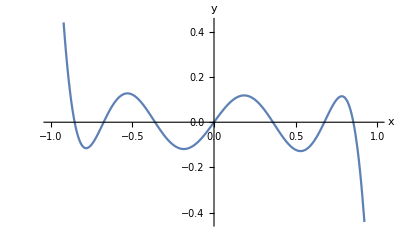

```mathematica
Plot[p,{x,-1,1},AxesLabel->{x,y}]
```

```mathematica
p/.x->0.8
```

0.108677

```mathematica
NSolve[p==0,x]
```

{{x→-1.39522},{x→-0.852542},{x→-0.675059},{x→-0.360622},{x→0.},{x→0.-3.0611 ⅈ},{x→0.+3.0611 ⅈ},{x→0.360622},{x→0.675059},{x→0.852542},{x→1.39522}}

```mathematica
N[Solve[p==0,x],4]
```

{{x→0},{x→-3.061 ⅈ},{x→3.061 ⅈ},{x→-0.3606},{x→0.3606},{x→-0.6751},{x→0.6751},{x→-0.8525},{x→0.8525},{x→-1.395},{x→1.395}}

## 5.2 Legendre Polynomials

```mathematica
LegendreP[3,x]
```

1/2 (-3 x+5 x^3)

```mathematica
Leg[n_]=1/(2^n n!)D[(x^2-1)^n,{x,n}]
```

(2^-n ∂_{x,n} (-1+x^2)^n)/(n!)

```mathematica
Leg[0]
```

1

```mathematica
Leg[1]
```

x

```mathematica
Leg[2]
```

1/8 (8 x^2+4 (-1+x^2))

```mathematica
Simplify[%]
```

1/2 (-1+3 x^2)

```mathematica
Simplify[Leg[3]]
```

1/2 x (-3+5 x^2)

```mathematica
Apart[Leg[3]]
```

-(3 x)/2+(5 x^3)/2

```mathematica
S=Table[Simplify[Leg[n]],{n,0,4}]
```

{1,x,1/2 (-1+3 x^2),1/2 x (-3+5 x^2),1/8 (3-30 x^2+35 x^4)}

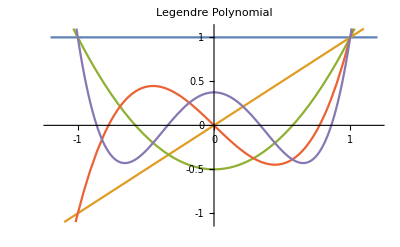

```mathematica
Plot[Evaluate[S],{x,-1.2,1.2},PlotRange->{-1.1,1.1},PlotLabel->"Legendre Polynomial",Ticks->{{-1,0,1},{-1,-0.5,0,0.5,1}}]
```

## 5.3 Legendre’s Differential Equation

```mathematica
Clear[y,n,m,s,a]
```

```mathematica
LegEq=(1-x^2)y''[x]-2x y'[x]+n(n+1)y[x]==0
```

n (1+n) y[x]-2 x y'[x]+(1-x^2) y''[x]==0

```mathematica
LegEq4=LegEq/.n->4
```

20 y[x]-2 x y'[x]+(1-x^2) y''[x]==0

```mathematica
DSolve[{LegEq4,y[0]==3/8,y'[0]==0},y[x],x]
```

{{y[x]→1/8 (3-30 x^2+35 x^4)}}

```mathematica
DSolve[{LegEq4,y[-1]==1,y[1]==1},y[x],x]
```

{{y[x]→1/8 (3-30 x^2+35 x^4)}}

```mathematica
ser=Sum[a[m]x^m,{m,s,s+2}]
```

x^s a[s]+x^(1+s) a[1+s]+x^(2+s) a[2+s]

```mathematica
(1-x^2)D[ser,x,x]-2x D[ser,x]+n(n+1)ser==0
```

(1-x^2) ((-1+s) s x^(-2+s) a[s]+s (1+s) x^(-1+s) a[1+s]+(1+s) (2+s) x^s a[2+s])-2 x (s x^(-1+s) a[s]+(1+s) x^s a[1+s]+(2+s) x^(1+s) a[2+s])+n (1+n) (x^s a[s]+x^(1+s) a[1+s]+x^(2+s) a[2+s])==0

```mathematica
temp=Simplify[%]
```

x^s (n (1+n) (a[s]+x (a[1+s]+x a[2+s]))-1/x^2(-1+x^2) ((-1+s) s a[s]+(1+s) x (s a[1+s]+(2+s) x a[2+s]))-2 (s a[s]+x ((1+s) a[1+s]+(2+s) x a[2+s])))==0

```mathematica
co=Coefficient[Expand[x^2temp[[1,2]]],x^2]
```

n a[s]+n^2 a[s]-s a[s]-s^2 a[s]+2 a[2+s]+3 s a[2+s]+s^2 a[2+s]

```mathematica
Solve[co==0,a[s+2]]
```

{{a[2+s]→(-n a[s]-n^2 a[s]+s a[s]+s^2 a[s])/(2+3 s+s^2)}}

```mathematica
a[s+2]==Factor[%[[1,1,2]]]
```

a[2+s]==((-n+s) (1+n+s) a[s])/((1+s) (2+s))

## 5.4 Orthogonality, Fourier-Legendre Series

```mathematica
Table[Table[Integrate[LegendreP[m,x]LegendreP[n,x],{x,-1,1}],{m,0,n}],{n,0,10}]
```

{{2},{0,2/3},{0,0,2/5},{0,0,0,2/7},{0,0,0,0,2/9},{0,0,0,0,0,2/11},{0,0,0,0,0,0,2/13},{0,0,0,0,0,0,0,2/15},{0,0,0,0,0,0,0,0,2/17},{0,0,0,0,0,0,0,0,0,2/19},{0,0,0,0,0,0,0,0,0,0,2/21}}

```mathematica
f=Sin[Pi x]
```

Sin[π x]

```mathematica
S=Sum[(2m+1)/2Integrate[f LegendreP[m,x],{x,-1,1}]"LegendreP"[m,x],{m,1,5}]
```

(3 LegendreP[1,x])/π+(7 (-15+π^2) LegendreP[3,x])/π^3+(11 (945-105 π^2+π^4) LegendreP[5,x])/π^5

```mathematica
S1=N[%]
```

0.95493 LegendreP[1.,x]-1.15824 LegendreP[3.,x]+0.21929 LegendreP[5.,x]

```mathematica
coeffs=Table[S1[[n,1]],{n,1,3}]
```

{0.95493,-1.15824,0.21929}

```mathematica
terms=Table[coeffs[[p]]LegendreP[2p-1,x],{p,1,3}]
```

{0.95493 x,-0.579121 (-3 x+5 x^3),0.0274112 (15 x-70 x^3+63 x^5)}

```mathematica
S2=terms[[1]]+terms[[2]]
```

0.95493 x-0.579121 (-3 x+5 x^3)

```mathematica
Expand[S2]
```

2.69229 x-2.8956 x^3

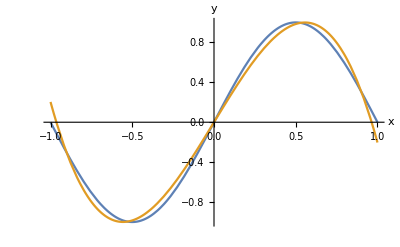

```mathematica
Plot[{f,S2},{x,-1,1},AxesLabel->{x,y}]
```

## 5.5 Frobenius Method

```mathematica
Clear[a,c,m,s,y]
```

```mathematica
ode1=x^2y''[x]+b x y'[x]+c y[x]==0
```

c y[x]+b x y'[x]+x^2 y''[x]==0

```mathematica
DSolve[ode1,y[x],x]
```

{{y[x]→x^(1/2 (-(-1+b)/(√c)-(√(1-2 b+b^2-4 c))/(√c)) √c) C[1]+x^(1/2 (-(-1+b)/(√c)+(√(1-2 b+b^2-4 c))/(√c)) √c) C[2]}}

```mathematica
ode2=x(x-1)y''[x]+(3x-1)y'[x]+y[x]==0
```

y[x]+(-1+3 x) y'[x]+(-1+x) x y''[x]==0

```mathematica
DSolve[ode2,y[x],x]
```

{{y[x]→C[1]/(1-x)-(C[2] Log[x])/(-1+x)}}

```mathematica
Simplify[%]
```

{{y[x]→(C[1]+C[2] Log[x])/(1-x)}}

```mathematica
ser=Sum[a[m]x^m,{m,s,s+2}]
```

x^s a[s]+x^(1+s) a[1+s]+x^(2+s) a[2+s]

```mathematica
x(x-1)D[ser,x,x]+(3x-1)D[ser,x]+ser==0
```

x^s a[s]+x^(1+s) a[1+s]+x^(2+s) a[2+s]+(-1+x) x ((-1+s) s x^(-2+s) a[s]+s (1+s) x^(-1+s) a[1+s]+(1+s) (2+s) x^s a[2+s])+(-1+3 x) (s x^(-1+s) a[s]+(1+s) x^s a[1+s]+(2+s) x^(1+s) a[2+s])==0

```mathematica
FullSimplify[%]
```

x^(-1+s) ((s^2 (-1+x)+x+2 s x) a[s]+x ((-(1+s)^2+(2+s)^2 x) a[1+s]+x (-(2+s)^2+(3+s)^2 x) a[2+s]))==0

```mathematica
co=Coefficient[Expand[%[[1,2]]],x]
```

a[s]+2 s a[s]+s^2 a[s]-a[1+s]-2 s a[1+s]-s^2 a[1+s]

```mathematica
Solve[%==0,a[s+1]]
```

{{a[1+s]→a[s]}}

```mathematica
ode3=x(1-x)y''[x]+2(1-2x)y'[x]-2y[x]==0
```

-2 y[x]+2 (1-2 x) y'[x]+(1-x) x y''[x]==0

```mathematica
DSolve[ode3,y[x],x]
```

{{y[x]→C[1]/(x-x^2)+C[2]/(1-x)}}

## 5.6 Bessel’s Equation, Bessel Functions

```mathematica
BES=x^2y''[x]+x y'[x]+(x^2-ν^2)y[x]==0
```

(x^2-ν^2) y[x]+x y'[x]+x^2 y''[x]==0

```mathematica
sol=DSolve[BES,y[x],x]
```

{{y[x]→BesselJ[ν,x] C[1]+BesselY[ν,x] C[2]}}

```mathematica
BES[[1]]/.ν->0
```

x^2 y[x]+x y'[x]+x^2 y''[x]

```mathematica
Simplify[%]/x
```

x y[x]+y'[x]+x y''[x]

```mathematica
sol/.{C[1]->1,C[2]->0,ν->0}
```

{{y[x]→BesselJ[0,x]}}

```mathematica
ser0=Series[%[[1,1,2]],{x,0,12}]
```

1-x^2/4+x^4/64-x^6/2304+x^8/147456-x^10/14745600+x^12/2123366400+O[x]^13

```mathematica
p0=Normal[%]
```

1-x^2/4+x^4/64-x^6/2304+x^8/147456-x^10/14745600+x^12/2123366400

```mathematica
sol/.{C[1]->1,C[2]->0,ν->1}
```

{{y[x]→BesselJ[1,x]}}

```mathematica
ser1=Series[%[[1,1,2]],{x,0,12}]
```

x/2-x^3/16+x^5/384-x^7/18432+x^9/1474560-x^11/176947200+O[x]^13

```mathematica
p1=Normal[%]
```

x/2-x^3/16+x^5/384-x^7/18432+x^9/1474560-x^11/176947200

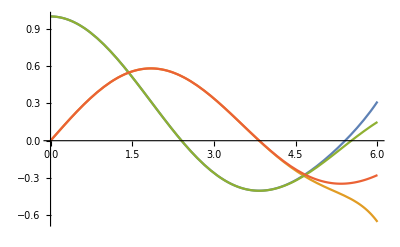

```mathematica
Plot[{p0,p1,BesselJ[0,x],BesselJ[1,x]},{x,0,6}]
```

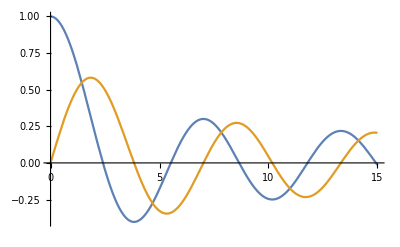

```mathematica
Plot[{BesselJ[0,x],BesselJ[1,x]},{x,0,15},Ticks->{{0,5,10,15},Automatic}]
```

```mathematica
x01appr=NSolve[p0==0,x]
```

{{x→-6.78143-5.6004 ⅈ},{x→-6.78143+5.6004 ⅈ},{x→-6.54585-1.72484 ⅈ},{x→-6.54585+1.72484 ⅈ},{x→-5.40592},{x→-2.40483},{x→2.40483},{x→5.40592},{x→6.54585-1.72484 ⅈ},{x→6.54585+1.72484 ⅈ},{x→6.78143-5.6004 ⅈ},{x→6.78143+5.6004 ⅈ}}

```mathematica
x01=SetPrecision[FindRoot[BesselJ[0,x]==0,{x,1}],10]
```

{x→2.404825558}

## --------------------TheEnd--------------------